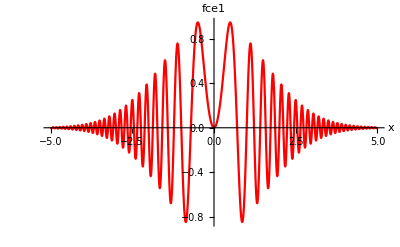

```mathematica
fce1[ω_,σ_,t_]:=Sin[ω*t]*E^(-t^2/(2*σ^2));
Plot[fce1[2*Pi*x,1.5,x],{x,-5,5},AxesLabel->{"x","fce1"},PlotStyle->{Red}]
(*Plot3D[fce1[2*Pi*x,1.5,x],{x,-5,5},{t,Infinity,Infinity},AxesLabel->Automatic,PlotStyle->{Red}]*)
```

```mathematica
uloha={-Subscript[x, 2]+3 Subscript[x, 1]==3,-6 Subscript[x, 1]+17 Subscript[x, 2]+2 Subscript[x, 3]==14,-21 Subscript[x, 1]+15 Subscript[x, 3]==3};
vyr=Subscript[x, 1]+Subscript[x, 2]-Subscript[x, 3];
vysl=Solve[uloha]
vyr/.vysl
```

{{x_1→323/239,x_2→252/239,x_3→500/239}}

{75/239}

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t]}}

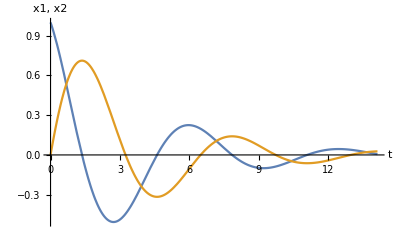

```mathematica
soustavaRovnic={x1'[t]==-x2[t]-0.5*x1[t],x2'[t]==x1[t]};
soustavaPodminek={x1[0]==1,x2[0]==0};
vsechnyRovnice=Union[soustavaRovnic,soustavaPodminek];
neznameRovnice={x1[t],x2[t]};
reseniRovnice=NDSolve[vsechnyRovnice,neznameRovnice,{t,0,9*Pi/2}]
Plot[Evaluate[neznameRovnice/.reseniRovnice],{t,0,9*Pi/2},AxesLabel->{"t","x1, x2"},PlotRange->All]
```